Math 9 Homework 6

Nhi Nguyen, Trang Nguyen, Melvin Chang

Problem 1

1.

```mathematica
i={1,5000,1};
```

```mathematica
w={0};
```

```mathematica
list={w};
```

```mathematica
f[w_]:=If[Abs[RandomInteger[w]]<0.5,w[End]+1,w[End]-1]
```

```mathematica
While[Abs[w]<10,w=f[w];AppendTo[list,w]]
```

```mathematica
v={}
```

{}

```mathematica
Do[ list={w};While[ Abs[w]<10, w=f[w];AppendTo[list,w]];AppendTo[v,Length[list]], {w,1,5000}]
```

2.

```mathematica
vMin=Min[v]
```

3.

```mathematica
vMax=Max[v]
```

4.

```mathematica
vMean=Mean[v]
```

5.

```mathematica
vMedian=Median[v]
```

6.

```mathematica
Graphics[Histogram[v]]
```

Problem 2

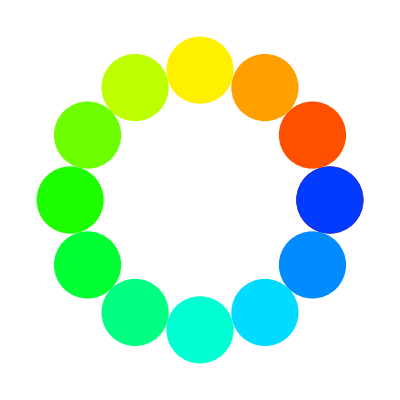

```mathematica
Graphics[Table[{Hue[i/10],Disk[{(Sqrt[6]+Sqrt[2])*Cos[i],(Sqrt[6]+Sqrt[2])*Sin[i]}]},{i,0,2*Pi,Pi/6}]]
```